# Dynamical Systems Analysis of Ellis and Maartens’ Emergent Universe

## Dimensionless Variables - 3D

```mathematica
vFlat=3*u^2-(ψ^2)/2
```

3 u^2-ψ^2/2

```mathematica
ψFlat=Sqrt[6*u^2-2*v]
```

√(6 u^2-2 v)

```mathematica
vFlatSurface=Plot3D[{vFlat},{u,-1,1},{ψ,-1,1},PlotStyle->{{Darker[Green],Opacity[0.5]}},Mesh->None,AxesLabel->{"u","ψ","v"},PlotPoints->200]
```

-Graphics3D-

```mathematica
deu:=u'=-u^2-(1/3)*(ψ^2-v)
deψ:=ψ'=-3*u*ψ-2*Sqrt[v]*(1-Sqrt[v])
dev:=v'=-2*ψ*Sqrt[v]*(1-Sqrt[v])
```

```mathematica
(*Solve the system of equations for the fixed points*)
FPs=Solve[{deu==0,deψ==0,dev==0},{u,ψ,v}]
```

{{u→0,ψ→0,v→0},{u→0,ψ→0,v→0},{u→-1/(√3),ψ→0,v→1},{u→1/(√3),ψ→0,v→1},{u→0,ψ→-1,v→1},{u→-1/(√3),ψ→0,v→1},{u→1/(√3),ψ→0,v→1},{u→0,ψ→1,v→1}}

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={u/.FPs[[1,1]],ψ/.FPs[[1,2]],v/.FPs[[1,3]]};
FP[2]={u/.FPs[[3,1]],ψ/.FPs[[3,2]],v/.FPs[[3,3]]};
FP[3]={u/.FPs[[4,1]],ψ/.FPs[[4,2]],v/.FPs[[4,3]]};
FP[4]={u/.FPs[[5,1]],ψ/.FPs[[5,2]],v/.FPs[[5,3]]};
FP[5]={u/.FPs[[8,1]],ψ/.FPs[[8,2]],v/.FPs[[8,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,5}];
```

```mathematica
FixedPointsPlot=ListPointPlot3D[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[deu,u],D[deu,ψ],D[deu,v]}, {D[deψ,u],D[deψ,ψ],D[deψ,v]},{D[dev,u],D[dev,ψ],D[dev,v]}}];
J//MatrixForm
```

(-2 u | -(2 ψ)/3 | 1/3
-3 ψ | -3 u | 2-1/(√v)
0 | 2 (-√v+v) | (2-1/(√v)) ψ)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{u->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]],v->FixedPoints[[i,3]]}]//MatrixForm,Simplify[Eigenvalues[J/.{u->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]],v->FixedPoints[[i,3]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{u->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]],v->FixedPoints[[i,3]]}]]//MatrixForm},{i,1,5}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvectors::inf: Input matrix contains an infinite entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0
0) | (0 | 0 | 1/3
0 | 0 | ComplexInfinity
0 | 0 | Indeterminate) | Eigenvalues[{{0,0,1/3},{0,0,ComplexInfinity},{0,0,Indeterminate}}] | Eigenvectors[{{0,0,1/3},{0,0,ComplexInfinity},{0,0,Indeterminate}}]
(-1/(√3)
0
1) | (2/(√3) | 0 | 1/3
0 | √3 | 1
0 | 0 | 0) | (√3
2/(√3)
0) | (0 | 1 | 0
1 | 0 | 0
-1/(2 √3) | -1/(√3) | 1)
(1/(√3)
0
1) | (-2/(√3) | 0 | 1/3
0 | -√3 | 1
0 | 0 | 0) | (-√3
-2/(√3)
0) | (0 | 1 | 0
1 | 0 | 0
1/(2 √3) | 1/(√3) | 1)
(0
-1
1) | (0 | 2/3 | 1/3
3 | 0 | 1
0 | 0 | -1) | (-√2
√2
-1) | (-(√2)/3 | 1 | 0
(√2)/3 | 1 | 0
-1/3 | 0 | 1)
(0
1
1) | (0 | -2/3 | 1/3
-3 | 0 | 1
0 | 0 | 1) | (-√2
√2
1) | ((√2)/3 | 1 | 0
-(√2)/3 | 1 | 0
1/3 | 0 | 1)

```mathematica
(3*u1[t]^2-ψ1[t]^2/2)
```

```mathematica
v1[t]
```

```mathematica
deut:=u1'[t]==-u1[t]^2-(1/3)*(ψ1[t]^2-(3*u1[t]^2-ψ1[t]^2/2))
deψt:=ψ1'[t]==-3*u1[t]*ψ1[t]-2*Sqrt[(3*u1[t]^2-ψ1[t]^2/2)]*(1-Sqrt[(3*u1[t]^2-ψ1[t]^2/2)])
devt:=v1'[t]==-2*ψ1[t]*Sqrt[(3*u1[t]^2-ψ1[t]^2/2)]*(1-Sqrt[(3*u1[t]^2-ψ1[t]^2/2)])
```

```mathematica
traj[u0_,ψ0_]=NDSolve[{deut,deψt,devt,u1[0]==u0,ψ1[0]==ψ0,v1[0]==3*u0^2-ψ0^2/2},{u1,ψ1,v1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition u0 is not a number or a rectangular array of numbers.

NDSolve[{u1'[t]==-u1[t]^2+1/3 (3 u1[t]^2-(3 ψ1[t]^2)/2),ψ1'[t]==-3 u1[t] ψ1[t]-2 √(3 u1[t]^2-ψ1[t]^2/2) (1-√(3 u1[t]^2-ψ1[t]^2/2)),v1'[t]==-2 ψ1[t] √(3 u1[t]^2-ψ1[t]^2/2) (1-√(3 u1[t]^2-ψ1[t]^2/2)),u1[0]==u0,ψ1[0]==ψ0,v1[0]==3 u0^2-ψ0^2/2},{u1,ψ1,v1},{t,-100,100}]

```mathematica
Sqrt[6*1^2-2*.5]
```

2.23607

```mathematica
sol[1]=traj[.5,.5]
```

NDSolve::ndsz: At t == -1.03887, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[2]=traj[.9,.5]
```

NDSolve::ndsz: At t == -1.37329, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[3]=traj[1,.4]
```

NDSolve::ndsz: At t == -0.963472, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
traj3D[1]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[1],{t,-1.03,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[2]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[2],{t,-1.36,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[3]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[3],{t,-0.962,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
trajectories=Table[traj3D[i],{i,1,3}];
```

```mathematica
Show[vFlatSurface,FixedPointsPlot,trajectories,AxesLabel->{"u","ψ","v"}]
```

-Graphics3D-

## Dimensionless Variables - 2D - V-ψ phase space - Expanding

```mathematica
Clear[ψ];
```

```mathematica
u=Sqrt[v/3+(ψ^2)/6]
```

√(v/3+ψ^2/6)

```mathematica
deψ:=ψ'=-3*u*ψ-2*Sqrt[v]*(1-Sqrt[v])
dev:=v'=-2*ψ*Sqrt[v]*(1-Sqrt[v])
```

```mathematica
(*Solve the system of equations for the fixed points*)
FPs=Solve[{deψ==0,dev==0},{ψ,v}]
```

{{ψ→0,v→0},{ψ→0,v→1},{ψ→-ⅈ √2,v→1},{ψ→ⅈ √2,v→1}}

```mathematica
FindRoot[{deψ==0,dev==0},{ψ,-1},{v,0}]
```

{ψ→-1.93365×10^-9,v→0.}

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={ψ/.FPs[[1,1]],v/.FPs[[1,2]]};
FP[2]={ψ/.FPs[[2,1]],v/.FPs[[2,2]]};
FP[3]={ψ/.FPs[[3,1]],v/.FPs[[3,2]]};
FP[4]={ψ/.FPs[[4,1]],v/.FPs[[4,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,4}];
```

```mathematica
FPsψvExpanding=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[deψ,ψ],D[deψ,v]},{D[dev,ψ],D[dev,v]}}];
J//MatrixForm
```

(-(√6 (v+ψ^2))/(√(2 v+ψ^2)) | 2-1/(√v)-(√(3/2) ψ)/(√(2 v+ψ^2))
2 (-√v+v) | (2-1/(√v)) ψ)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{ψ->FixedPoints[[i,1]],v->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{ψ->FixedPoints[[i,1]],v->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{ψ->FixedPoints[[i,1]],v->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,4}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 √6 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 √(3/2) ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Eigenvectors::mindet: Input matrix contains an indeterminate entry.

Eigenvalues::inf: Input matrix contains an infinite entry.

Eigenvectors::inf: Input matrix contains an infinite entry.

Eigenvalues::inf: Input matrix contains an infinite entry.

Eigenvectors::inf: Input matrix contains an infinite entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0) | (Indeterminate | Indeterminate
0 | Indeterminate) | Eigenvalues[{{Indeterminate,Indeterminate},{0,Indeterminate}}] | Eigenvectors[{{Indeterminate,Indeterminate},{0,Indeterminate}}]
(0
1) | (-√3 | 1
0 | 0) | (-√3
0) | (1 | 0
1/(√3) | 1)
(-ⅈ √2
1) | (ComplexInfinity | ComplexInfinity
0 | -ⅈ √2) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{0,-ⅈ √2}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{0,-ⅈ √2}}]
(ⅈ √2
1) | (ComplexInfinity | ComplexInfinity
0 | ⅈ √2) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{0,ⅈ √2}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{0,ⅈ √2}}]

```mathematica
PhaseSpaceψvExpanding=StreamPlot[{deψ,dev},{ψ,-1,1},{v,-1,1}];
```

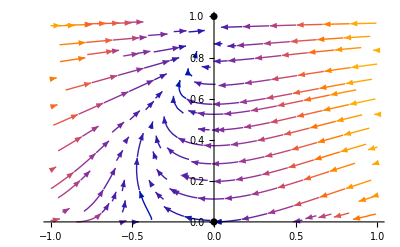

```mathematica
Show[FPsψvExpanding,PhaseSpaceψvExpanding]
```

## Dimensionless Variables - 2D - V-ψ phase space - Contracting

```mathematica
Clear[ψ];
```

```mathematica
u=-Sqrt[v/3+(ψ^2)/6]
```

-√(v/3+ψ^2/6)

```mathematica
deψ:=ψ'=-3*u*ψ-2*Sqrt[v]*(1-Sqrt[v])
dev:=v'=-2*ψ*Sqrt[v]*(1-Sqrt[v])
```

```mathematica
(*Solve the system of equations for the fixed points*)
FPs=Solve[{deψ==0,dev==0},{ψ,v}]
```

{{ψ→0,v→0},{ψ→0,v→1},{ψ→-ⅈ √2,v→1},{ψ→ⅈ √2,v→1}}

```mathematica
FindRoot[{deψ==0,dev==0},{ψ,1},{v,0.05}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{ψ→0.0100182+0.00282231 ⅈ,v→1.63777×10^-9+3.21799×10^-9 ⅈ}

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={ψ/.FPs[[1,1]],v/.FPs[[1,2]]};
FP[2]={ψ/.FPs[[2,1]],v/.FPs[[2,2]]};
FP[3]={ψ/.FPs[[3,1]],v/.FPs[[3,2]]};
FP[4]={ψ/.FPs[[4,1]],v/.FPs[[4,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,4}];
```

```mathematica
FPsψvExpanding=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[deψ,ψ],D[deψ,v]},{D[dev,ψ],D[dev,v]}}];
J//MatrixForm
```

((√6 (v+ψ^2))/(√(2 v+ψ^2)) | 2-1/(√v)+(√(3/2) ψ)/(√(2 v+ψ^2))
2 (-√v+v) | (2-1/(√v)) ψ)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{ψ->FixedPoints[[i,1]],v->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{ψ->FixedPoints[[i,1]],v->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{ψ->FixedPoints[[i,1]],v->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,4}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 √6 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 √(3/2) ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Eigenvectors::mindet: Input matrix contains an indeterminate entry.

Eigenvalues::inf: Input matrix contains an infinite entry.

Eigenvectors::inf: Input matrix contains an infinite entry.

Eigenvalues::inf: Input matrix contains an infinite entry.

Eigenvectors::inf: Input matrix contains an infinite entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0) | (Indeterminate | Indeterminate
0 | Indeterminate) | Eigenvalues[{{Indeterminate,Indeterminate},{0,Indeterminate}}] | Eigenvectors[{{Indeterminate,Indeterminate},{0,Indeterminate}}]
(0
1) | (√3 | 1
0 | 0) | (√3
0) | (1 | 0
-1/(√3) | 1)
(-ⅈ √2
1) | (ComplexInfinity | ComplexInfinity
0 | -ⅈ √2) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{0,-ⅈ √2}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{0,-ⅈ √2}}]
(ⅈ √2
1) | (ComplexInfinity | ComplexInfinity
0 | ⅈ √2) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{0,ⅈ √2}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{0,ⅈ √2}}]

```mathematica
PhaseSpaceψvExpanding=StreamPlot[{deψ,dev},{ψ,-1,1},{v,-1,1}];
```

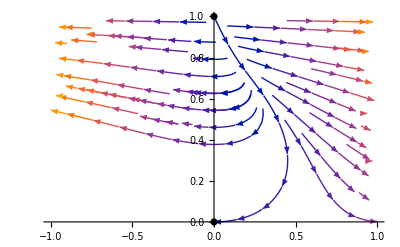

```mathematica
Show[FPsψvExpanding,PhaseSpaceψvExpanding]
```

## Dimensionless Variables - 2D - u-ψ Phase Space

```mathematica
Clear[ψ];
```

```mathematica
v=3*u^2-(ψ^2)/2
```

3 u^2-ψ^2/2

```mathematica
deu:=u'=-u^2-(1/3)*(ψ^2-v)
deψ:=ψ'=-3*u*ψ-2*Sqrt[v]*(1-Sqrt[v])
```

```mathematica
(*Solve the system of equations for the fixed points*)
FPs=Solve[{deu==0,deψ==0},{u,ψ}]
```

{{u→0,ψ→0},{u→-1/(√3),ψ→0},{u→1/(√3),ψ→0}}

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={u/.FPs[[1,1]],ψ/.FPs[[1,2]]};
FP[2]={u/.FPs[[2,1]],ψ/.FPs[[2,2]]};
FP[3]={u/.FPs[[3,1]],ψ/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,3}];
```

```mathematica
FPsuψ=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[deu,u],D[deu,ψ]}, {D[deψ,u],D[deψ,ψ]}}];
J//MatrixForm
```

(0 | -ψ
-3 ψ+u (12-6/(√(3 u^2-ψ^2/2))) | -3 u+ψ (-2+1/(√(3 u^2-ψ^2/2))))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{u->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{u->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{u->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,3}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Eigenvectors::mindet: Input matrix contains an indeterminate entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0) | (0 | 0
Indeterminate | Indeterminate) | Eigenvalues[{{0,0},{Indeterminate,Indeterminate}}] | Eigenvectors[{{0,0},{Indeterminate,Indeterminate}}]
(-1/(√3)
0) | (0 | 0
-2 √3 | √3) | (√3
0) | (0 | 1
1 | 2)
(1/(√3)
0) | (0 | 0
2 √3 | -√3) | (-√3
0) | (0 | 1
1 | 2)

```mathematica
PhaseSpaceuψ=StreamPlot[{deu,deψ},{u,-1,1},{ψ,-1,1}];
```

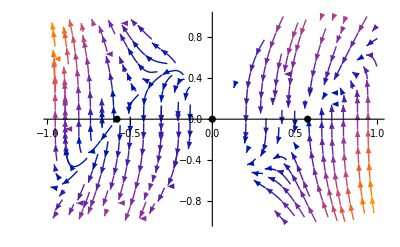

```mathematica
Show[FPsuψ,PhaseSpaceuψ,PlotRange->All]
```